### Hamiltonian: regularization of the Coulomb potential

Potential energy operator

```mathematica
𝒱(r__,r1__,r2__,α_):=-1/(√(Norm[{r}-{r1}]^2+α^2))-1/(√(Norm[{r}-{r2}]^2+α^2))+1/Norm[{r2}-{r1}]
```

Kinetic energy operator:

```mathematica
𝒦(ψ_)(r__):=-1/2 ψ(r){r}
```

Hamiltonian operator:

```mathematica
ℋ(ψ_)(r__,r1__,r2__,α_):=ψ(r) 𝒱(r,r1,r2,α)+𝒦(ψ)(r)
```

A parameter α is necessary to regularize the potential energy to avoid the potential energy to blow up at singularities.

### Eigensystem for the left(right) system

The function eigensystem[l,𝓇,ne], finds ne eigenvalues of the H_2^+ for a internuclear distance 𝓇 in a computational box of length 2ℓ+𝓇 :

```mathematica
eigensystem3dLR[ℓ_,𝓇_,ne_,a_]:=
SortBy[
Transpose[
NDEigensystem[{ℋ[ψ][x,-𝓇/2,𝓇/2,a],DirichletCondition[ψ[x]==0,True]},ψ,
{x,𝓇/2,ℓ},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]],
First]
```

```mathematica
esysdLR=eigensystem3dLR[30.,3.,60,0.001];
```

```mathematica
esysdLR[[1]]
```

{-0.398629,InterpolatingFunction[{{1.5, 30.}}, <>]}

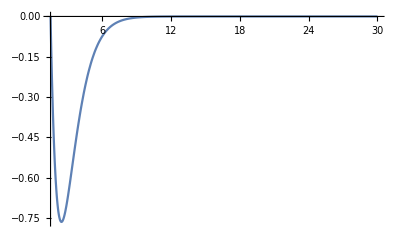

```mathematica
Plot[{esysdLR[[1,2]][x],esysn[[1,2]][x]},{x,0.5,30},PlotRange->All]
```

### Eigensystem for the central system

```mathematica
eigensystem3dC[𝓇_,ne_,a_]:=
SortBy[
Transpose[
NDEigensystem[{ℋ[ψ][x,-𝓇/2,𝓇/2,a],DirichletCondition[ψ[x]==0,True]},ψ,
{x,-𝓇/2,𝓇/2},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]],
First]
```

```mathematica
esysdC=eigensystem3dC[3.,60,0.001];
```

```mathematica
esysdC[[1]]
```

{-0.816853,InterpolatingFunction[{{-1.5, 1.5}}, <>]}

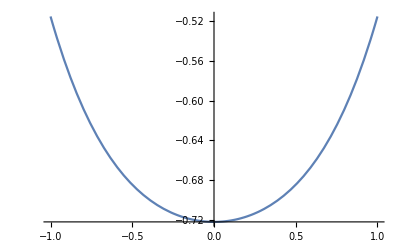

```mathematica
Plot[{esysdC[[1,2]][x]},{x,-1,1},PlotRange->All]
```

#### Matching the three solutions

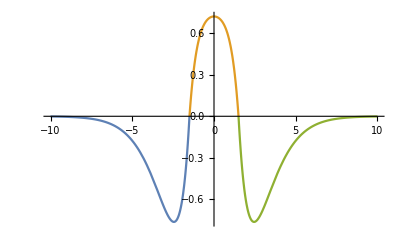

```mathematica
Plot[{esysdLR[[1,2]][-x],-esysdC[[1,2]][x],esysdLR[[1,2]][x]},{x,-10,10.},PlotRange->All]
```

#### The ground state energies as function of the internuclear distance for left-right and central systems

```mathematica
eLR[r_]:=eigensystem3dLR[30.,r,60,0.001]
```

```mathematica
eC[r_]:=eigensystem3dC[r,60,0.001]
```

```mathematica
fullsys=Table[{r,eLR[r],eC[r]},{r,0.6,8.2,0.1}];
```

```mathematica
stateLR=Table[Interpolation[Table[{fullsys[[i,1]],fullsys[[i,2,j,1]]},{i,1,Length[fullsys]}]],{j,1,10}];
```

```mathematica
stateC=Table[Interpolation[Table[{fullsys[[i,1]],fullsys[[i,3,j,1]]},{i,1,Length[fullsys]}]],{j,1,10}];
```

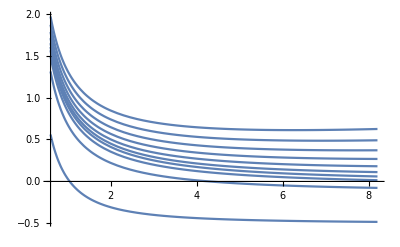

```mathematica
plotLR=Plot[Table[stateLR[[i]][x],{i,1,10}],{x,0.6,8.2}]
```

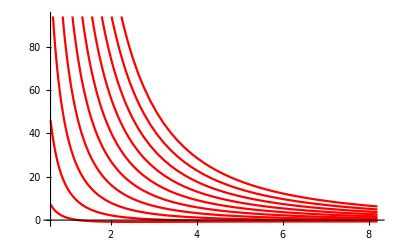

```mathematica
plotC=Plot[Table[stateC[[i]][x],{i,1,10}],{x,0.6,8.2},PlotStyle->Red]
```

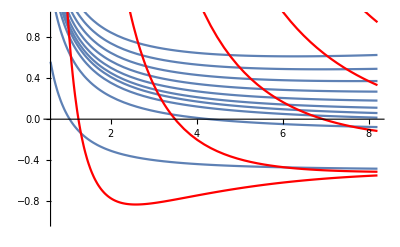

```mathematica
Show[plotLR,plotC,PlotRange->{-1,1}]
```

#### Intersection between curves gives good Born-Oppenheimer states

```mathematica
ground={r,stateC[[1]][r],eC[r],eLR[r]}/.FindRoot[stateC[[1]][r]==stateLR[[1]][r],{r,2}];
```

InterpolatingFunction::dmval: Input value {-1.74689} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::ivar: -9.99959 is not a valid variable.

General::ivar: -9.59143 is not a valid variable.

General::ivar: -9.18326 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

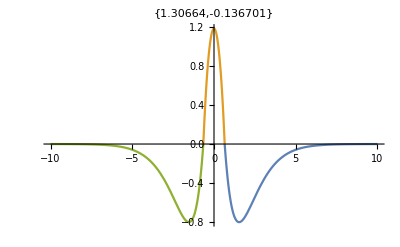

```mathematica
Plot[{ground[[4,1,2]][x],-ground[[3,1,2]][x],ground[[4,1,2]][-x],D[ground[[4,1,2]][x],x]},{x,-10,10},PlotRange->All,PlotLabel->{ground[[1]],ground[[2]]}]
```

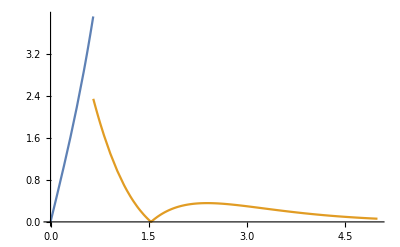

```mathematica
Plot[{Abs[D[ground[[3,1,2]][r],r]]/.r->y,Abs[D[ground[[4,1,2]][r],r]]/.r->y},{y,0,5},PlotRange->All]
```

```mathematica
dgC=Abs[D[ground[[3,1,2]][x],x]]/.x->ground[[1]]/2
```

3.91432

```mathematica
dgLR=Abs[D[ground[[4,1,2]][x],x]]/.x->ground[[1]]/2
```

2.34513

General::ivar: -9.99959 is not a valid variable.

General::ivar: -9.59143 is not a valid variable.

General::ivar: -9.18326 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

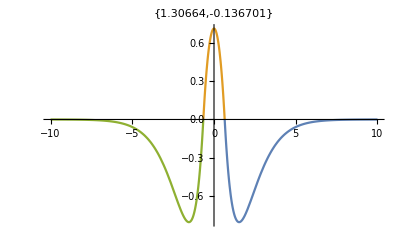

```mathematica
Plot[{ground[[4,1,2]][x],-ground[[3,1,2]][x]*(dgLR/dgC),ground[[4,1,2]][-x],D[ground[[4,1,2]][x],x]},{x,-10,10},PlotRange->All,PlotLabel->{ground[[1]],ground[[2]]}]
```

```mathematica
ground[[2]]
```

-0.228172

```mathematica
(dgLR/dgC) (* the central wf must be multiplied by this number to mtch derivatives at boundaries *)
```

0.599116

```mathematica
(1+1+(dgLR/dgC)^2) (* the function with matching derivatives at boundaries now have this norm *)
```

2.35894

```mathematica
Sqrt[1/(1+1+(dgLR/dgC)^2)](* the global wf must be multiplied by this quantity to have it normalized *)
```

0.651091

```mathematica
excited={r,stateC[[1]][r],eC[r],eLR[r]}/.FindRoot[stateC[[1]][r]==stateLR[[2]][r],{r,2}];
```

InterpolatingFunction::dmval: Input value {-16.6308} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.13692} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

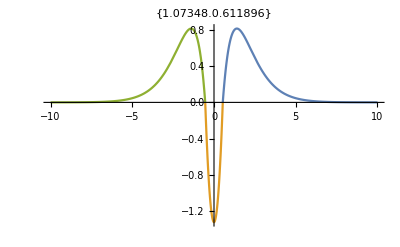

```mathematica
Plot[{excited[[3,1,2]][x],excited[[4,1,2]][x],excited[[3,1,2]][-x]},{x,-10,10},PlotRange->All,PlotLabel->{excited[[1]].excited[[2]]}]
```

```mathematica
(*Manipulate[
GraphicsGrid@
Partition[
(es↦Table[
Show[
Plot[{es⟦i,1⟧+(es⟦i,2⟧[x])},{x,-ℓ,ℓ},
Filling->{1->es⟦i,1⟧,2-> Bottom},PlotPoints->20,PlotRange->{le,le+ΔE}]
],
{i,1,4}
])@
eigensystem3[ℓ,𝓇,ne,0.1],
2],
{{ℓ,10,"Box Length"},10,20,1},
{{𝓇,2,"Bond Length"},1.,6.,0.5},
{{ne,40,"Number of eigenfunctions"},40,100,5},
{{le,-2,"Lowest Energy"},-10,0,0.5},
{{ΔE,3,"Energy range"},1,20,2}
]*)
```